# Universal Estimator

## Parameter range adjustment

For convenience, we want to work with parameters  ∈ (0,1) and map them to the parameters in the original range.
For that, we can use the Logistic function and its Logit inverse.

#### The Logistic function

The standard Logistic function, σ(x), defined in (-∞, ∞) and yields values in (0,1):

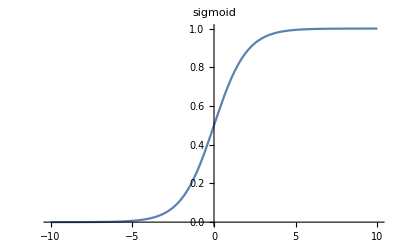

```mathematica
Sigmoid[x_]:=1/(1+ⅇ^-x)
Plot[Sigmoid[x], {x, -10, +10}, PlotLabel->HoldForm[sigmoid]]
```

#### The Logit function

The Logit  is the inverse of the Logistic function σ(x), defined in (0,1) and yields values in (-∞, ∞).
Let’s find the inverse:
σ(x) = y =  1/(1+e^-x) ⇒  1+e^-x = 1/y  ⇒  e^-x = 1/y-1=(1-y)/y  ⇒  log(e^-x)=log((1-y)/y)  ⇒  -x = log((1-y)/y)  ⇒  x = log(y/(1-y)) = σ^-1(x)

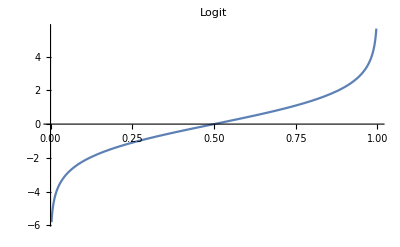

```mathematica
Logit[x_]:= Log[x/(1-x)]
Plot[Logit[x], {x, 0, 1}, PlotLabel->HoldForm[Logit]]
```

### Range Adjuster

We define an Adjuster function which returns another function that maps a parameter in the range  (0,1) to the range  (low, high) of the original distribution.
We can use the Logistic function and its Logit inverse as follows:
Let
	h(t) = Logit(t) , t ∈ (0,1)
Than
	h^-1(d) = Sigmoid(d) , d ∈ (-∞, ∞)

```mathematica
Adjuster[low_, high_]:=With[{LOW=Sigmoid[low],HIGH=Sigmoid[high]}, Function[{t},Logit[LOW+t(HIGH-LOW)]]]
```

### Test Adjuster

For example, we can create an Adjuster for the range [2,5] and call it with values ∈ [0,1]

```mathematica
adj=Adjuster[2, 5];
Print[adj[0.01]];
```

2.01076

```mathematica
Print[adj[0.99]];
```

4.84348

Plot of the adjuster output in the range [0,1]

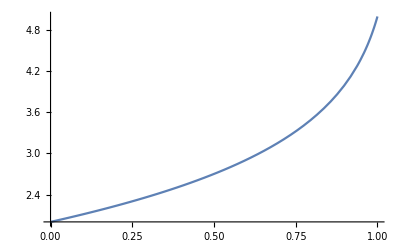

```mathematica
Print[Plot[adj[x], {x,0,1}]]
```

## Generate data

Arguments:

nSamples: number of samples

M: number of observations in each sample

f: the function to generate samples

ranges: an array [d X 2] of parameter ranges (e.g. for 2 parameters: [[0, 10], [0, ∞]])

bins: number of bins in histograms (default: max[samples]+1)

Returns:

a table of associations: histogram -> params (over all samples)

```mathematica
GenerateData[nSamples_, M_, f_, ranges_, bins_:-1]:= 
Module[{nParams, adjusters, params, samples, nbins, histograms},

(*number of parameters*)
nParams=Dimensions[ranges][[1]];

(*generate an adapter for each parameter range*)
adjusters=Table[Adjuster[ranges[[i,1]],ranges[[i,2]]],{i,1,nParams}];

(*generate N parameters cube in the range (0,1)*)
params=Table[adjusters[[j]][RandomReal[{0,1}]],{i,1,nSamples},{j,1,nParams}];

(*generate N samples from the parameters*)
samples=Table[f[params[[i]],M],{i,1,nSamples}];

(*create a histogram from each sample*)
nbins=If [bins>0,bins,Max[samples]+1];
h[x_]:=HistogramList[x, {0,nbins,1}][[2]];

(*output*)
Table[h@samples[[i]]-> params[[i]], {i, 1, nSamples}]
]
```

Test GenerateData

```mathematica
YuleSimon[{α_,β_}, M_]:=RandomVariate[WaringYuleDistribution[α,β],M];
YuleSimonRanges = {{2,3},{0,10}};

LogNormal[{μ_,σ_}, M_]:=RandomVariate[LogNormalDistribution[μ,σ],M];
LogNormalRanges = {{1,3},{0,5}};

Print[];
Print["YuleSimon"];
YuleSimonData = GenerateData[5,10,YuleSimon, YuleSimonRanges];
Print[YuleSimonData//TableForm];

Print[];
Print["LogNormal"];
LogNormalData = GenerateData[5,10,LogNormal, LogNormalRanges];
Print[LogNormalData//TableForm];
```

YuleSimon

{6,1,1,1,1}→{2.23044,1.12256}
{6,1,1,0,2}→{2.6047,1.20873}
{9,1,0,0,0}→{2.78256,0.748601}
{6,3,0,1,0}→{2.51205,1.05387}
{8,2,0,0,0}→{2.92212,0.143533}

LogNormal

{1,3,1,1,1,0,1,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{1.31398,0.688837}
{0,0,2,0,0,1,1,0,1,0,0,2,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0}→{2.27362,0.9967}
{0,1,2,3,1,0,0,0,1,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}→{1.50744,1.5266}
{2,1,1,1,0,0,0,0,0,0,1,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1}→{1.17302,1.37718}
{1,0,2,2,3,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→{1.37149,0.405126}

## DNN

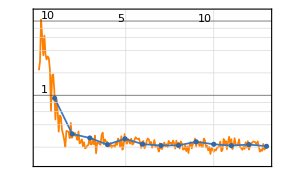
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:208  rounds:13  time:23s  examples/s:590
data | ,,  training examples:1000  validation examples:250  processed examples:13312  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.09×10^-1
validation | ,,  loss:2.05×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
CreateNet[bins_, nParams_]:=( 
NetChain[{
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp],
(*DropoutLayer[0.2],*)
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp],
(*DropoutLayer[0.2],*)
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp], 
(*DropoutLayer[0.2],*)
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp], 
(*DropoutLayer[0.2],*)
LinearLayer[nParams]},
"Input"->bins, 
"Output" -> nParams]
)

M = 256;
nSamples = 1000;
trainSet=GenerateData[nSamples,M,YuleSimon, YuleSimonRanges];
bins = Length@trainSet[[1]][[1]];
valSet=GenerateData[nSamples/4,M,YuleSimon, YuleSimonRanges, bins];
nParams=Dimensions[YuleSimonRanges][[1]];
net = NetInitialize@CreateNet[bins, nParams];
(*Print[NetGraph[net]];*)
trained=NetTrain[net,trainSet,All, Method->"ADAM", 
ValidationSet->valSet, 
LossFunction->MeanAbsoluteLossLayer[]];
trained
```

## Experiments

#### Define some longtail distributions

```mathematica
(*Sample M observations from the Yule distribution with shape parameters α and β.*)
YuleSimonRV[{α_,β_}, M_]:=RandomVariate[WaringYuleDistribution[α,β],M];

(*Sample M observations from the PowerLaw distribution with domain parameter k and shape parameter a.*)
PowerLawRV[{k_,a_}, M_]:=RandomVariate[PowerDistribution[k,a],M];

(*distributions*)
distributions = Association[
"yulesimon" -> Association["dist"->YuleSimonRV, "ranges"->{{2,3},{0,10}}, "M"->256],
"powerlaw" -> Association["dist"->PowerLawRV, "ranges"->{{1,10},{0,10}}, "M"->256]
];
```

```mathematica
(*test association*)
dist = distributions["yulesimon"];
f = dist["dist"];
ranges = dist["ranges"];
M = dist["M"];
f[ranges[[1]], M]
```

{0,0,17,0,0,3,0,0,2,5,2,4,0,7,12,1,1,0,2,6,0,22,0,8,0,0,2,1,0,0,0,0,0,0,0,2,12,0,0,0,0,0,6,0,2,5,1,4,2,2,3,2,3,0,0,2,0,4,0,0,8,3,0,0,0,26,1,8,2,0,9,5,0,0,1,0,0,0,0,0,2,0,0,0,6,1,0,0,1,1,0,1,2,1,2,0,3,1,0,0,6,0,0,0,0,4,0,10,1,0,0,0,1,2,0,1,1,3,0,1,3,8,1,15,3,16,2,0,3,6,0,1,1,13,3,1,0,9,1,0,21,0,58,23,4,2,3,1,0,0,4,2,0,2,6,0,1,3,1,0,1,5,0,3,0,1,1,0,1,2,1,7,0,2,1,0,0,3,0,1,0,0,0,0,1,2,0,0,0,3,0,1,0,1,2,0,0,1,0,0,1,3,0,20,0,0,4,0,5,4,37,4,0,1,1,1,0,11,12,0,1,0,0,1,1,4,1,0,3,4,0,3,1,3,0,5,8,0,17,2,0,3,2,7,2,0,0,6,11,1,21,8,0,10,3,0}

#### Run experiments

Run the experiment for each longtail distribution.

• Let P = the number of parameters for the distribution.
  Create a P-dimensional mesh on the unit square, with a resolution of 0.1 (i.e: 0.1, 0.2, ... , 0.9)
  The mesh is a cube of size 9^P (e.g: 81 cell matrix for 2 params)

• Generate learning samples for each data point in the mesh (using GenerateData defined above).

• At each mesh point:
	• Train a NN model at each mesh point for predicting the parameters of the distribution at that point.
	• Run several predictions of the parameters at that point and average the prediction error.
	• Compute the Cramer-Raw bound for the mesh point.
	• Record the relation  (prediction error)/(Cramer-Raw bound)
• Plot a surface of the relation above at each mesh point, hopefully showing a value around 2 at each point.

```mathematica
RunExperiment[distributions_, distname_]:=
Module[{dist, f, ranges, M, adjuster1, adjuster2, mesh},

(*get definitions for specified distribution*)
dist = distributions[distname];
f = dist["dist"];
ranges = dist["ranges"];
M = dist["M"];

(*generate an adapter for each parameter range*)
adjuster1=Adjuster[ranges[[1,1]],ranges[[1,2]]];
adjuster2=Adjuster[ranges[[2,1]],ranges[[2,2]]];

(*create a parameters mesh*)
mesh = Table[{adjuster1[i/10],adjuster2[j/10]},{i,1,9 },{j,1,9 }];
(*train mesh points*)

(*output*)

]
```